# Plotting

SimulationTools allows you to use the standard Mathematica plotting functions on DataTables and DataRegions.  Where appropriate, information about the coordinate range of the data is determined automatically, avoiding the need to specify it manually as would be the case when using data in lists only.  Here we show some examples of what can be done.

## Array Plot

To demonstrate plotting 2D simulation data, we use the example data from a numerical relativity binary black hole simulation:

```mathematica
phi=ReadGridFunction[$SimulationToolsTestSimulation,"phi","xy",RefinementLevel->3,Iteration->6144]
```

DataRegion[ML_BSSN::phi.01.01,<43,83>,{{-0.75,9.75},{-10.25,10.25}}]

The resulting 2D DataRegion can be plotted directly with ArrayPlot:

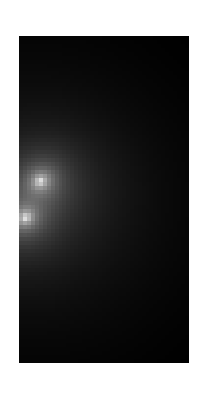

```mathematica
ArrayPlot[phi]
```

Mathematica chooses the colour scheme automatically.  We can improve the information content and appearance of the plot further:

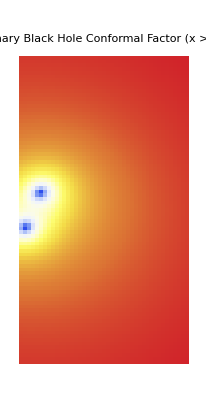

```mathematica
arrayPlot=ArrayPlot[phi,
ColorFunction->ColorData[{"TemperatureMap",{0,1}}],
FrameTicks->True,
FrameLabel->{"xCell[""]","y"},
PlotLabel->"Binary Black Hole Conformal Factor (x > 0)"]
```

## Height-map plot

```mathematica
ListPlot3D[phi,PlotRange->All]
```

-Graphics3D-

## Contour Plot

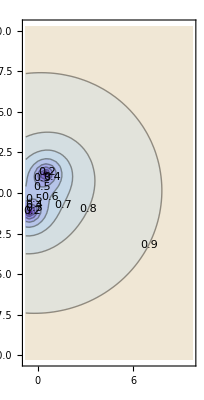

```mathematica
ListContourPlot[phi,PlotRange->All,AspectRatio->Automatic,ContourLabels->True]
```